# Beyond typology beyond optimization Part 3

## e) Re-Generation Classifier

The code is structured as follows:
Cells in yellow are variables that need to be check, always run first 
Cells in red contain code to load data, always after the yellow cells
Cells in blue contain code, always run in order
Cells in white are to check the consistency of the data, not need to run

## Functions

```mathematica
ImportEdgeConnection[edgeNode_]:=
Block[{edgesConection},
edgesConection=Import[NotebookDirectory[]<>edgeNode];
edgesConection=1+#&/@#&/@edgesConection;
Return@edgesConection
]
```

## Training a Classifier

#### Label your data

```mathematica
user="Karla";

edgesConnection=ImportEdgeConnection[edgeNode];
subset=Import[NotebookDirectory[]<>"filteredSubset"<>user<>".m"];
```

Import your label data

```mathematica
listNonPrefer=Import[NotebookDirectory[]<>"formsNonPrefer.m"];
listPrefer=Import[NotebookDirectory[]<>"formsPrefer.m"];
```

```mathematica
preferForms=subset[[All,#]]&/@listPrefer;

white1=If[0.0001≤ Abs@#≥ 0,#,a]&/@#&/@preferForms[[All,"force"]];
blueRed1=If[#<0,Blue,Red,White]&/@#&/@white1;

blueRedOri=If[#<0,Blue,Red]&/@#&/@preferForms[[All,"force"]];

cellsPerfer=Table[Graphics3D[
{Thickness[Abs[preferForms[[All,"force"]]][[i,#]]/700],
blueRed1[[i,#]],Line[Partition[preferForms[[All,"points"]][[i]],3][[edgesConnection[[#]]]]]
}&/@Range@Length@edgesConnection,Boxed->False(*,ViewPoint->Top*)],{i,1100,1140}];

Grid[Partition[cellsPerfer,6],Spacings->{0,0}]
```

```mathematica
input=subset["input"];

perferInput=input[[#]]&/@listPrefer;
nonPreferInput=input[[#]]&/@listNonPrefer;

prefer=Thread[perferInput->"1"];
nonPrefer=Thread[nonPreferInput->"0"];

rules=Join[prefer,nonPrefer];
```

```mathematica
rules[[1;;10]]//Column
```

{40.,2.,0.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,-0.4,6.,0.,-1.8,6.,0.,-5.3,6.,0.,-5.1,6.,0.,1.8,1.,0.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,0.8,0.,1.,3.7,0.,1.,1.9,0.,1.,5.9,0.,1.,4.3,1.,0.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,-0.6,6.,0.,-4.6,6.,0.,-4.8,6.,0.,3.6,6.,0.,-0.7,1.,1.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,1.,6.,1.,-0.4,6.,1.,5.3,6.,1.,4.9,6.,1.,3.3,1.,0.,40.,14.,800.,4.}→1
{40.,2.,90.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,-1.7,2.,0.,0.2,2.,0.,-5.7,2.,0.,-1.8,2.,0.,-2.7,1.,1.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,-1.6,4.,1.,-3.5,4.,1.,2.,4.,1.,2.,4.,1.,1.2,1.,1.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.9,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,2.7,0.,1.,-5.2,0.,1.,0.1,0.,1.,-0.3,0.,1.,-3.1,1.,0.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.8,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,1.5,0.,0.,3.2,0.,0.,1.2,0.,0.,-5.8,0.,0.,0.7,1.,1.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.8,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,-1.1,0.,1.,-2.1,0.,1.,-2.8,0.,1.,-5.9,0.,1.,5.,1.,0.,40.,14.,800.,4.}→1
{40.,2.,0.,0.,0.,0.,-0.8,-1.,0.,0.,-1.,-1.,0.,0.,-1.,0.,0.,-1.,0.,0.,-1.,0.6,0.,0.,0.6,2.,0.,-3.4,2.,0.,1.5,2.,0.,-5.4,2.,0.,5.5,1.,1.,40.,14.,800.,4.}→1

1345

```mathematica
rules=Join[RandomSample[prefer,Min@Counts@Sort[rules[[All,2]]]],RandomSample[nonPrefer,Min@Counts@Sort[rules[[All,2]]]]];
```

```mathematica
Counts@rules[[All,2]]
```

<|1→1345,0→1345|>

```mathematica
rules=RandomSample[rules,Length@rules];
```

#### Create a Classifier

```mathematica
{testData,trainData}=TakeDrop[rules,Ceiling[Length[rules]/10]];
```

```mathematica
classifier=Classify[trainData,Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

```mathematica
Export[NotebookDirectory[]<>"classifier"<>user<>".wmlf",classifier];
```

```mathematica
classifier=Import[NotebookDirectory[]<>"classifier"<>user<>".wmlf"];
```

```mathematica
Information[classifier]
```

Classifier information
Data type | NumericalVector (length: 43)
Classes | ,,01
Accuracy | (85.22.3) %
Method | GradientBoostedTrees
Single evaluation time | 3.93 ms/example
Batch evaluation speed | 39.3 examples/ms
Loss | 0.346 ± 0.028
Model memory | 394. kB
Training examples used | 2421 examples
Training time | 3.8 s
 |

Extra characteristics of the Classifier

```mathematica
cm=ClassifierMeasurements[classifier,testData];
```

```mathematica
cm["Accuracy"]
```

0.869888

```mathematica
cm["Precision"]
```

<|0→0.95,1→0.822485|>

```mathematica
cm["Recall"]
```

<|0→0.76,1→0.965278|>

```mathematica
cm["F1Score"]
```

<|0→0.844444,1→0.888179|>

```mathematica
cm["FalseNegativeRate"]
```

<|0→0.24,1→0.0347222|>

```mathematica
cm["FalsePositiveRate"]
```

<|0→0.0347222,1→0.24|>

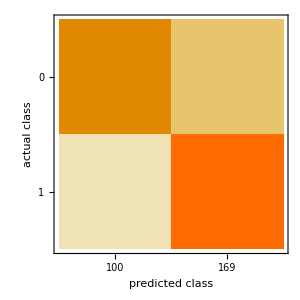

```mathematica
cm["ConfusionMatrixPlot"]
```

## Predicting results

#### Generate input values

With this cells you are creating random input values, based on the range from the generated design options

```mathematica
classifier=Import[NotebookDirectory[]<>"classifier"<>user<>".wmlf"];
```

```mathematica
input=subset["input"];

list=Transpose[input];
minMax=N@MinMax[#]&/@list;
```

With samples you generate the amount of input to classify

```mathematica
samples=10000;

posInteger={4,5,6,9,10,13,14,16,17,19,20,23,24,26,27,29,30,32,33,35,36,38,39,42,43};
posReal=Complement[Range[43],posInteger];

minMaxInt=minMax[[#]]&/@posInteger;
minMaxReal=minMax[[#]]&/@posReal;

randomInputInt=Quiet@RandomInteger[minMaxInt[[#]]]&/@Range@Length@minMaxInt&/@Range[samples];
randomInputReal=RandomReal[minMaxReal[[#]]]&/@Range@Length@minMaxReal&/@Range[samples];

int=Thread[posInteger->#]&/@randomInputInt;
real=Thread[posReal->#]&/@randomInputReal;

inputs=Join[{int[[#]],real[[#]]}]&/@Range@Length@int;
inputs=Flatten[#]&/@inputs;
inputs=Sort[#]&/@inputs;
randomInput=Values[#]&/@inputs;
```

With this cell you are predicting the class from the generated inputs

```mathematica
start=Now;
result=classifier[#,{"TopProbabilities",1}]&/@randomInput;

data=Thread[result->randomInput];
byClass=GatherBy[data,#[[1,1,1]]&];
Now-start
```

47.0447 s

Check how the results and define a class Prefer depending if the first list has label 1 put 1 otherwise 2

```mathematica
classPrefer=1;
byClass[[classPrefer]][[1;;10]]//TableForm
```

{1→0.666077}→{40.,2.,56.9122,0,0,0,-0.810626,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,1.91665,4,0,-3.11961,5,1,1.28892,4,1,1.97104,6,1,-2.64197,1,0,35.3235,22.0351,760,4}
{1→0.800666}→{40.,2.,72.0115,0,0,0,-0.765743,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,0.993257,2,1,0.729178,6,1,-2.23132,6,0,-5.43633,3,0,-3.68074,1,1,37.4791,19.4327,759,5}
{1→0.537315}→{40.,2.,28.3402,0,0,0,-0.801856,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-0.349258,1,0,-4.90334,5,1,-4.32944,1,1,0.370505,2,0,0.445363,1,0,37.7204,19.0109,779,5}
{1→0.737662}→{40.,2.,31.3359,0,0,0,-0.58084,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,0.204131,4,1,-0.749155,1,0,-3.21174,2,1,3.9174,4,1,5.24844,1,1,39.6158,17.9105,733,5}
{1→0.732982}→{40.,2.,78.5566,0,0,0,-0.807842,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-1.65336,0,0,-2.77469,1,0,0.102267,0,0,-1.92809,5,1,5.93127,1,0,35.2923,19.5386,619,5}
{1→0.706752}→{40.,2.,26.2622,0,0,0,-0.732018,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-0.465896,4,0,1.2087,6,0,-1.42701,1,0,-5.75218,4,0,2.66256,1,1,38.605,19.0199,761,6}
{1→0.651388}→{40.,2.,36.0482,0,0,0,-0.700241,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-0.554158,4,0,-3.28656,3,1,-0.865824,6,1,-2.28762,6,1,0.201085,1,0,33.7616,20.5182,656,4}
{1→0.5504}→{40.,2.,21.8998,0,0,0,-0.506749,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-1.70378,2,0,2.11859,3,0,3.92319,0,1,-2.3259,5,0,0.957086,1,1,34.3498,15.659,661,6}
{1→0.765036}→{40.,2.,80.8058,0,0,0,-0.855817,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,0.243565,1,0,-5.68168,5,1,-1.66489,0,1,2.25579,2,0,-3.94287,1,2,39.4929,17.2598,702,4}
{1→0.762219}→{40.,2.,40.7966,0,0,0,-0.631125,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-2.01191,1,1,-0.725686,3,1,-3.00125,2,1,0.763685,3,1,-5.04666,1,1,36.6076,23.2151,777,6}

Take only the best results

```mathematica
higherProbability[x_]:=If[x>0.85,1,0];
split=higherProbability/@Flatten[Values[Keys[byClass[[classPrefer]]]]];
pos=Position[split,1];
```

Check which come first (0 or 1)

```mathematica
inputPrefer=Values[byClass][[classPrefer]][[#]]&/@pos;
```

```mathematica
inputPrefer[[1;;10]]//Column
```

{{40.,2.,28.9937,0,0,0,-0.881433,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-1.31303,1,1,4.46452,5,1,-4.27402,0,0,5.32349,1,0,-2.1734,1,2,38.8813,14.2534,726,5}}
{{40.,2.,1.2373,0,0,0,-0.73744,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-0.995618,2,0,-2.2537,1,1,-2.62207,4,0,1.51946,1,0,-3.92866,1,1,36.836,15.7639,790,4}}
{{40.,2.,16.7735,0,0,0,-0.864296,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-2.34968,5,1,4.95693,0,1,-3.28488,6,0,-0.764128,5,0,-3.65557,1,2,37.0318,17.0859,724,4}}
{{40.,2.,64.5082,0,0,0,-0.529844,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-2.26959,3,1,-4.48029,4,0,3.40784,2,0,-3.00013,0,0,-0.835726,1,1,38.812,14.4574,652,4}}
{{40.,2.,83.7008,0,0,0,-0.543989,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,2.20548,4,0,-5.3605,4,0,-0.0226427,6,0,-1.23334,2,1,-4.10113,1,1,34.8347,22.0651,702,4}}
{{40.,2.,43.4905,0,0,0,-0.828386,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,0.957223,6,0,-1.02156,5,1,-1.28091,4,0,-4.99258,2,0,-5.07177,1,1,38.1324,17.0172,664,4}}
{{40.,2.,36.8443,0,0,0,-0.513438,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,1.71519,5,1,-4.55869,0,0,-0.466686,4,1,-4.7957,1,0,-4.41815,1,2,37.1376,14.2477,703,5}}
{{40.,2.,86.4264,0,0,0,-0.766413,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,0.0460206,4,0,3.78983,5,1,-5.99846,1,1,-0.827636,4,1,-3.82415,1,0,39.5737,16.7881,612,4}}
{{40.,2.,51.3836,0,0,0,-0.574862,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,-1.36863,4,1,4.35814,3,1,-5.11396,1,1,-4.3202,6,0,5.09901,1,0,33.5328,24.8547,763,4}}
{{40.,2.,33.5262,0,0,0,-0.648591,-1.,0,0,-1.,-1.,0,0,-1.,0,0,-1.,0,0,-1.,0.6,0,0,1.84487,6,0,-5.45995,2,0,2.26862,6,1,-2.90594,1,1,-2.51825,1,2,33.4815,17.7016,666,5}}

```mathematica
inputPrefer//Length
```

337

```mathematica
Export[NotebookDirectory[]<>"inputPrefer"<>user<>".csv",inputPrefer];
```

With the exporting inputs, you can now go to the CEM generator and only generate the forms you prefer, so you can start the whole process again! Return to Part1